```mathematica
Import["https://raw.githubusercontent.com/drjjmc/ampGraphTools_mma/master/ampGraphTools/ampGraphTools.m"]
```

Welcome to ampGraphTools, version 0.43, 
a work in progress, but fairly simple implementation of
ideas in http://arxiv.org/abs/arXiv:1506.00974 and refs 
therein. - dr.jjmc@gmail.com.

```mathematica
possGraphs=treesToLoops[{Atree[{k[1],k[2],l[1],l[2],l[3]}],
Atree[{-l[3],-l[2],-l[1],k[3],k[4]}]}];
```

```mathematica
Grid[mathematicaGraph/@possGraphs//Partition[#,6]&]
```

-Graphics-

```mathematica
contributingGraphs=Select[possGraphs,!internalOneLoopTriangleQ[#]&&!internalOneLoopBubbleQ[#]&&!internalOneLoopTadpoleQ[#]&];
```

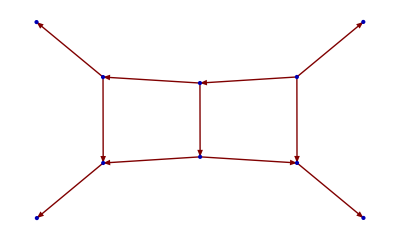
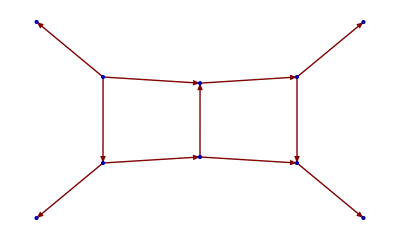
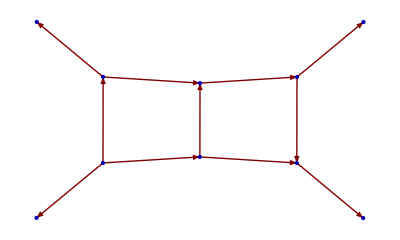

```mathematica
(doMomentaPlot/@contributingGraphs)/.in[_]:>""/.l[a_]:>Style[l[a],{Blue}]
```